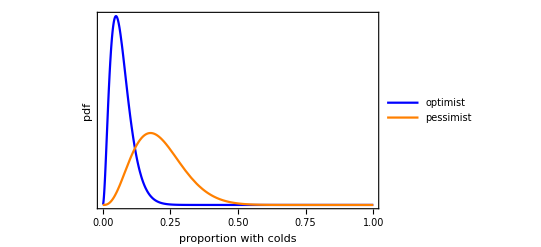

```mathematica
g1=Plot[{PDF[BetaDistribution[3,40],x],PDF[BetaDistribution[4,15],x]},{x,0,1},PlotRange->Full,PlotStyle->{Blue,Orange},FrameLabel->{"proportion with colds","pdf"},Frame->{True,True,False,False},BaseStyle->{FontSize->14},FrameTicks->{True,False},PlotLegends->Placed[{"optimist","pessimist"},Center]]
```

```mathematica
realData= RandomVariate[BinomialDistribution[100,0.18],{10}];
```

```mathematica
pOptimistGivenData =NIntegrate[PDF[BetaDistribution[3,40],p]*Likelihood[BinomialDistribution[100,p],realData],{p,0,1}]
pPessimistGivenData =NIntegrate[PDF[BetaDistribution[4,15],p]*Likelihood[BinomialDistribution[100,p],realData],{p,0,1}]
```

1.67185×10^-13

1.00171×10^-12

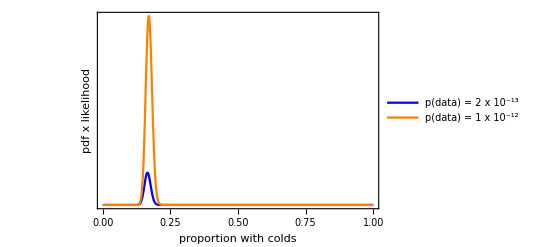

```mathematica
g3=Plot[{PDF[BetaDistribution[3,40],p]*Likelihood[BinomialDistribution[100,p],realData],PDF[BetaDistribution[4,15],p]*Likelihood[BinomialDistribution[100,p],realData]},{p,0,1},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->14},PlotLegends->Placed[{"p(data) = 2 x 10^-13","p(data) = 1 x 10^-12"},Center],FrameLabel->{"proportion with colds","pdf x likelihood"},PlotStyle->{Blue,Orange}]
```

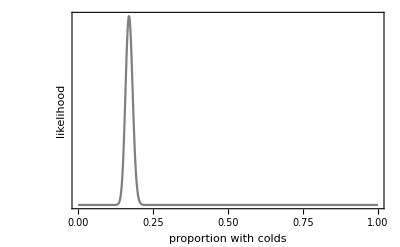

```mathematica
g2=Plot[Likelihood[BinomialDistribution[100,p],realData],{p,0,1},PlotRange->Full,PlotStyle->Gray,Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->14},FrameLabel->{"proportion with colds","likelihood"}]
```

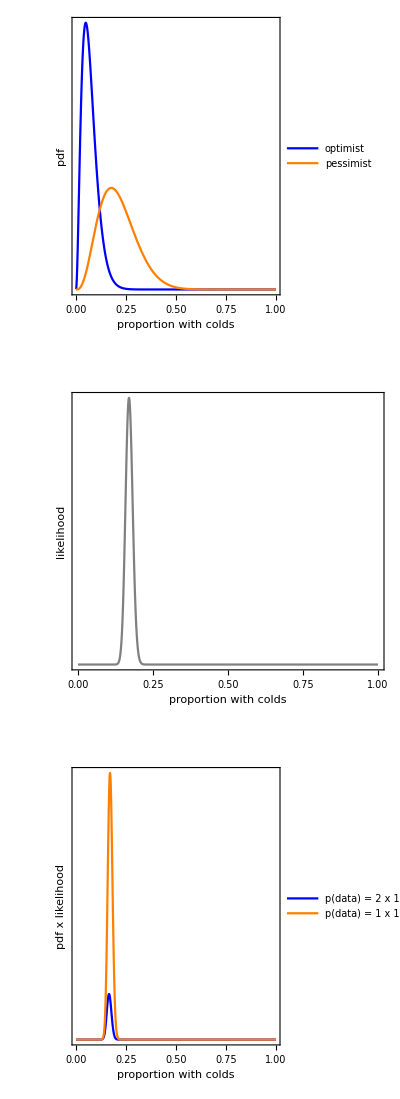

```mathematica
gFinal=Show[GraphicsColumn[{g1,g2,g3}],ImageSize->400]
```

```mathematica
Export["Posterior_bayesFactorFluEpidemiologist.pdf",gFinal]
```

Posterior_bayesFactorFluEpidemiologist.pdf

```mathematica
realData
```

{22,18,18,12,16,15,21,19,14,15}

```mathematica
pPessimistGivenData /pOptimistGivenData
```

5.99163